```mathematica
(* LOAD VARIABLES ----------------------
loads all functions and data (made in this file and evaluated previously) into memory so you don't have to run them again *)
Get[StringReplace[NotebookFileName[],".nb"->", variables.mx"]];
```

```mathematica
(* SAVE VARIABLES ----------------
Save the variables after evaluating them initially so you don't have to re-evaluate them every time *)
DumpSave[StringReplace[NotebookFileName[],".nb"->", variables.mx"],"Global`"];
```

```mathematica
AppendTo[$Path,ToFileName[{$HomeDirectory,"Dropbox","Academic","Code"}]];
<<BlochSVD`
```

```mathematica
comm[x_,y_]:=x.y-y.x
```

```mathematica
acomm[x_,y_]:=x.y+y.x
```

```mathematica
tPauliBasis3=Table[KroneckerProduct[pf[[i]],pf[[j]],pf[[k]]],{i,4},{j,4},{k,4}];
```

```mathematica
ghz=({{1, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 1}})/2;
```

```mathematica
w=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 1, 0, 1, 0, 0, 0}, {0, 1, 1, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 1, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})/3;
```

```mathematica
Eigenvalues[({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}})/2]
```

{-1/2,1/2,1/2,1/2,0,0,0,0}

```mathematica
Eigenvalues[ghz]
```

{1,0,0,0,0,0,0,0}

```mathematica
Eigenvalues[({{0, 0, 0, 0, 0, 1, 1, 0}, {0, 1, 1, 0, 0, 0, 0, 0}, {0, 1, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})/3]
```

{2/3,-(√2)/3,(√2)/3,1/3,0,0,0,0}

```mathematica
(*Define projection function to get Bloch components r from density matrix rho *)
rho2r3[rho_]:=Chop[Table[Tr[rho.tPauliBasis3[[i,j,k]]],{i,4},{j,4},{k,4}]];
```

```mathematica
(*the reverse operation =: get the density matrix rho from the Bloch matrix r *)
r2rho3[r_]:=Chop[Total[r*tPauliBasis3,3]/8];
```

```mathematica
(*Define projection function on too Dirac basis, differs from rho2r just in factor of 1/4
it is applied to nondensity matrices, e.g. operators *)
inPauliBasis[mat_]:=Simplify[Table[Tr[mat.tPauliBasis[[i,j,k]]]/8,{i,4},{j,4},{k,4}]];
```

```mathematica
(*the reverse operation of diracBasis*)
constructOpertor[pB_]:=Total[pB*tPauliBasis,3];
```

```mathematica
(* represent it in 3 colours, RGB for each bloch vector ... then the 2d matrices Cyan Magenta Yellow, then the 3d tensor white *)
```

```mathematica
(* can we get positivity inequalities as a RECURSION RELATION? *)
```

```mathematica
wR=rho2r[w]
```

({1,0,0,1/3} | {0,2/3,0,0} | {0,0,2/3,0} | {1/3,0,0,-1/3}
{0,2/3,0,0} | {2/3,0,0,2/3} | {0,0,0,0} | {0,2/3,0,0}
{0,0,2/3,0} | {0,0,0,0} | {2/3,0,0,2/3} | {0,0,2/3,0}
{1/3,0,0,-1/3} | {0,2/3,0,0} | {0,0,2/3,0} | {-1/3,0,0,-1})

```mathematica
Table[Print[wR[[i]]],{i,4}];
```

(1 | 0 | 0 | 1/3
0 | 2/3 | 0 | 0
0 | 0 | 2/3 | 0
1/3 | 0 | 0 | -1/3)

(0 | 2/3 | 0 | 0
2/3 | 0 | 0 | 2/3
0 | 0 | 0 | 0
0 | 2/3 | 0 | 0)

(0 | 0 | 2/3 | 0
0 | 0 | 0 | 0
2/3 | 0 | 0 | 2/3
0 | 0 | 2/3 | 0)

(1/3 | 0 | 0 | -1/3
0 | 2/3 | 0 | 0
0 | 0 | 2/3 | 0
-1/3 | 0 | 0 | -1)

```mathematica
f[dm[{2,2,1}]/3,{0,0,-1/3},{0,0,1/3},-1]
```

{16/9,0,0}

```mathematica
f[dm[{2,2,1}]/3,{0,0,-1/3},{0,0,1/3},1]
```

{16/9,-16/27,-256/81}

```mathematica
ghzR=rho2r[ghz]
```

({1,0,0,0} | {0,0,0,0} | {0,0,0,0} | {0,0,0,1}
{0,0,0,0} | {0,1,0,0} | {0,0,-1,0} | {0,0,0,0}
{0,0,0,0} | {0,0,-1,0} | {0,-1,0,0} | {0,0,0,0}
{0,0,0,1} | {0,0,0,0} | {0,0,0,0} | {1,0,0,0})

```mathematica
Table[Print[ghzR[[i]]],{i,4}];
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | -1 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
(* check positivity and entanglment of system once one subsystem is traced *)
```

```mathematica
f[dm[{0,0,1}],{0,0,0},{0,0,0},-1]
```

{2,0,0}

```mathematica
Pi/3
```

π/3

```mathematica
N[%]
```

1.0472

```mathematica
N[√3/2] 60
```

51.9615

```mathematica
(* cyclic permute *)
```

```mathematica
per=KroneckerProduct[({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}}),IdentityMatrix[2]].KroneckerProduct[IdentityMatrix[2],({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}})]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* Eggeling Werner Def *)
R3=(per-perᵀ)I/√3
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ/(√3) | 0 | -ⅈ/(√3) | 0 | 0 | 0
0 | -ⅈ/(√3) | 0 | 0 | ⅈ/(√3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/(√3) | ⅈ/(√3) | 0
0 | ⅈ/(√3) | -ⅈ/(√3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ/(√3) | 0 | 0 | -ⅈ/(√3) | 0
0 | 0 | 0 | -ⅈ/(√3) | 0 | ⅈ/(√3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Tr[R3.R3]
```

4

```mathematica
R0=(2 IdentityMatrix[8]-per-perᵀ)/3
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2/3 | -1/3 | 0 | -1/3 | 0 | 0 | 0
0 | -1/3 | 2/3 | 0 | -1/3 | 0 | 0 | 0
0 | 0 | 0 | 2/3 | 0 | -1/3 | -1/3 | 0
0 | -1/3 | -1/3 | 0 | 2/3 | 0 | 0 | 0
0 | 0 | 0 | -1/3 | 0 | 2/3 | -1/3 | 0
0 | 0 | 0 | -1/3 | 0 | -1/3 | 2/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Tr[R0.R0]
```

4

```mathematica
Rp=IdentityMatrix[8]-R0
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 1/3 | 0 | 1/3 | 0 | 0 | 0
0 | 1/3 | 1/3 | 0 | 1/3 | 0 | 0 | 0
0 | 0 | 0 | 1/3 | 0 | 1/3 | 1/3 | 0
0 | 1/3 | 1/3 | 0 | 1/3 | 0 | 0 | 0
0 | 0 | 0 | 1/3 | 0 | 1/3 | 1/3 | 0
0 | 0 | 0 | 1/3 | 0 | 1/3 | 1/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Tr[Rp.Rp]
```

4

```mathematica
(* to treat Eggeling and Werner's r_k as a coefficient, I must divide R_k by Tr[R_k.R_k], since EW coefficients are not normalized.. Therefore: *)
```

```mathematica
rho2r3[R3]/Tr[R3.R3]
```

({0,0,0,0} | {0,0,0,0} | {0,0,0,0} | {0,0,0,0}
{0,0,0,0} | {0,0,0,0} | {0,0,0,1/(√3)} | {0,0,-1/(√3),0}
{0,0,0,0} | {0,0,0,-1/(√3)} | {0,0,0,0} | {0,1/(√3),0,0}
{0,0,0,0} | {0,0,1/(√3),0} | {0,-1/(√3),0,0} | {0,0,0,0})

```mathematica
(* indeed the maximum r_3 can be is 1, because that is 1/√3 of the levi civita *)
```

```mathematica
rho2r3[IdentityMatrix[8]]
```

({8,0,0,0} | {0,0,0,0} | {0,0,0,0} | {0,0,0,0}
{0,0,0,0} | {0,0,0,0} | {0,0,0,0} | {0,0,0,0}
{0,0,0,0} | {0,0,0,0} | {0,0,0,0} | {0,0,0,0}
{0,0,0,0} | {0,0,0,0} | {0,0,0,0} | {0,0,0,0})

```mathematica
rho2r3[R0]/Tr[R0.R0]
```

({1,0,0,0} | {0,-1/3,0,0} | {0,0,-1/3,0} | {0,0,0,-1/3}
{0,-1/3,0,0} | {-1/3,0,0,0} | {0,0,0,0} | {0,0,0,0}
{0,0,-1/3,0} | {0,0,0,0} | {-1/3,0,0,0} | {0,0,0,0}
{0,0,0,-1/3} | {0,0,0,0} | {0,0,0,0} | {-1/3,0,0,0})

```mathematica
rho2r3[Rp]/Tr[Rp.Rp]
```

({1,0,0,0} | {0,1/3,0,0} | {0,0,1/3,0} | {0,0,0,1/3}
{0,1/3,0,0} | {1/3,0,0,0} | {0,0,0,0} | {0,0,0,0}
{0,0,1/3,0} | {0,0,0,0} | {1/3,0,0,0} | {0,0,0,0}
{0,0,0,1/3} | {0,0,0,0} | {0,0,0,0} | {1/3,0,0,0})

```mathematica
rho2r3[Rp-R0]
```

({0,0,0,0} | {0,8/3,0,0} | {0,0,8/3,0} | {0,0,0,8/3}
{0,8/3,0,0} | {8/3,0,0,0} | {0,0,0,0} | {0,0,0,0}
{0,0,8/3,0} | {0,0,0,0} | {8/3,0,0,0} | {0,0,0,0}
{0,0,0,8/3} | {0,0,0,0} | {0,0,0,0} | {8/3,0,0,0})

```mathematica
per+perᵀ
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2)

```mathematica
rho2r3[per+perᵀ]
```

({4,0,0,0} | {0,4,0,0} | {0,0,4,0} | {0,0,0,4}
{0,4,0,0} | {4,0,0,0} | {0,0,0,0} | {0,0,0,0}
{0,0,4,0} | {0,0,0,0} | {4,0,0,0} | {0,0,0,0}
{0,0,0,4} | {0,0,0,0} | {0,0,0,0} | {4,0,0,0})

```mathematica
rho2r3[KroneckerProduct[({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}}),IdentityMatrix[2]]]
```

```mathematica
KroneckerProduct[({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}}),IdentityMatrix[2]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* so my two candidate states are:
1) I did LHV for, just core levi civita with coeff 1/2*1/√3, this matches r3=1/2 rp=1/2 (r0=1/2)?
2) The extreme one,  core levi civita with coeff 1/√3 and bipartite -1/3 identity, this matches r3=1 rp=0 (r0=1)
```

```mathematica
r0 and r- .. need to extract the I from there ...
```

```mathematica
state1=(R0/Tr[R0.R0]+Rp/Tr[Rp.Rp]+R3/Tr[R3.R3])/2
```

(1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/8 | ⅈ/(8 √3) | 0 | -ⅈ/(8 √3) | 0 | 0 | 0
0 | -ⅈ/(8 √3) | 1/8 | 0 | ⅈ/(8 √3) | 0 | 0 | 0
0 | 0 | 0 | 1/8 | 0 | -ⅈ/(8 √3) | ⅈ/(8 √3) | 0
0 | ⅈ/(8 √3) | -ⅈ/(8 √3) | 0 | 1/8 | 0 | 0 | 0
0 | 0 | 0 | ⅈ/(8 √3) | 0 | 1/8 | -ⅈ/(8 √3) | 0
0 | 0 | 0 | -ⅈ/(8 √3) | 0 | ⅈ/(8 √3) | 1/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8)

```mathematica
Eigenvalues[state1]
```

{1/4,1/4,1/8,1/8,1/8,1/8,0,0}

```mathematica
rho2r3[state1]
```

({1,0,0,0} | {0,0,0,0} | {0,0,0,0} | {0,0,0,0}
{0,0,0,0} | {0,0,0,0} | {0,0,0,1/(2 √3)} | {0,0,-1/(2 √3),0}
{0,0,0,0} | {0,0,0,-1/(2 √3)} | {0,0,0,0} | {0,1/(2 √3),0,0}
{0,0,0,0} | {0,0,1/(2 √3),0} | {0,-1/(2 √3),0,0} | {0,0,0,0})

```mathematica
(* partial transpose *)
state1pt=r2rho3[({{{1,0,0,0}, {0,0,0,0}, {0,0,0,0}, {0,0,0,0}}, {{0,0,0,0}, {0,0,0,0}, {0,0,0,1/(2 √3)}, {0,0,1/(2 √3),0}}, {{0,0,0,0}, {0,0,0,-1/(2 √3)}, {0,0,0,0}, {0,1/(2 √3),0,0}}, {{0,0,0,0}, {0,0,-1/(2 √3),0}, {0,-1/(2 √3),0,0}, {0,0,0,0}}})]
```

(1/8 | 0 | 0 | ⅈ/(8 √3) | 0 | -ⅈ/(8 √3) | 0 | 0
0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/8 | 0 | ⅈ/(8 √3) | 0 | 0 | ⅈ/(8 √3)
-ⅈ/(8 √3) | 0 | 0 | 1/8 | 0 | -ⅈ/(8 √3) | 0 | 0
0 | 0 | -ⅈ/(8 √3) | 0 | 1/8 | 0 | 0 | -ⅈ/(8 √3)
ⅈ/(8 √3) | 0 | 0 | ⅈ/(8 √3) | 0 | 1/8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0
0 | 0 | -ⅈ/(8 √3) | 0 | ⅈ/(8 √3) | 0 | 0 | 1/8)

```mathematica
Eigenvalues[state1pt]
```

{1/4,1/4,1/8,1/8,1/8,1/8,0,0}

```mathematica
(* has positive PT .. consistent with biseparable but may not be .. so not good *)
```

```mathematica
state2=R0/Tr[R0.R0]+R3/Tr[R3.R3]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | -1/12+ⅈ/(4 √3) | 0 | -1/12-ⅈ/(4 √3) | 0 | 0 | 0
0 | -1/12-ⅈ/(4 √3) | 1/6 | 0 | -1/12+ⅈ/(4 √3) | 0 | 0 | 0
0 | 0 | 0 | 1/6 | 0 | -1/12-ⅈ/(4 √3) | -1/12+ⅈ/(4 √3) | 0
0 | -1/12+ⅈ/(4 √3) | -1/12-ⅈ/(4 √3) | 0 | 1/6 | 0 | 0 | 0
0 | 0 | 0 | -1/12+ⅈ/(4 √3) | 0 | 1/6 | -1/12-ⅈ/(4 √3) | 0
0 | 0 | 0 | -1/12-ⅈ/(4 √3) | 0 | -1/12+ⅈ/(4 √3) | 1/6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Eigenvalues[state2]
```

{1/2,1/2,0,0,0,0,0,0}

```mathematica
Simplify[rho2r3[state2]]
```

({1,0,0,0} | {0,-1/3,0,0} | {0,0,-1/3,0} | {0,0,0,-1/3}
{0,-1/3,0,0} | {-1/3,0,0,0} | {0,0,0,1/(√3)} | {0,0,-1/(√3),0}
{0,0,-1/3,0} | {0,0,0,-1/(√3)} | {-1/3,0,0,0} | {0,1/(√3),0,0}
{0,0,0,-1/3} | {0,0,1/(√3),0} | {0,-1/(√3),0,0} | {-1/3,0,0,0})

```mathematica
(* partial transpose *)
state2pt=r2rho3[({{{1,0,0,0}, {0,-1/3,0,0}, {0,0,1/3,0}, {0,0,0,-1/3}}, {{0,-1/3,0,0}, {-1/3,0,0,0}, {0,0,0,1/(√3)}, {0,0,1/(√3),0}}, {{0,0,1/3,0}, {0,0,0,-1/(√3)}, {-1/3,0,0,0}, {0,1/(√3),0,0}}, {{0,0,0,-1/3}, {0,0,-1/(√3),0}, {0,-1/(√3),0,0}, {-1/3,0,0,0}}})]
```

(0 | 0 | 0 | 1/8 (-2/3+(2 ⅈ)/(√3)) | 0 | 1/8 (-2/3-(2 ⅈ)/(√3)) | 0 | 0
0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/6 | 0 | 1/8 (-2/3+(2 ⅈ)/(√3)) | 0 | 0 | 1/8 (-2/3+(2 ⅈ)/(√3))
1/8 (-2/3-(2 ⅈ)/(√3)) | 0 | 0 | 1/6 | 0 | 1/8 (-2/3-(2 ⅈ)/(√3)) | 0 | 0
0 | 0 | 1/8 (-2/3-(2 ⅈ)/(√3)) | 0 | 1/6 | 0 | 0 | 1/8 (-2/3-(2 ⅈ)/(√3))
1/8 (-2/3+(2 ⅈ)/(√3)) | 0 | 0 | 1/8 (-2/3+(2 ⅈ)/(√3)) | 0 | 1/6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0
0 | 0 | 1/8 (-2/3-(2 ⅈ)/(√3)) | 0 | 1/8 (-2/3+(2 ⅈ)/(√3)) | 0 | 0 | 0)

```mathematica
Eigenvalues[state2pt]
```

{1/12 (1+√13),1/12 (1+√13),1/12 (1-√13),1/12 (1-√13),1/6,1/6,1/6,1/6}

```mathematica
(* so state two has a negative partial transpose across an bipartition, meaning it has bipartite entanglement 

equations 26c) e) f) in Eggelein and Werner 2001 UxUxU invariant paper *)
```

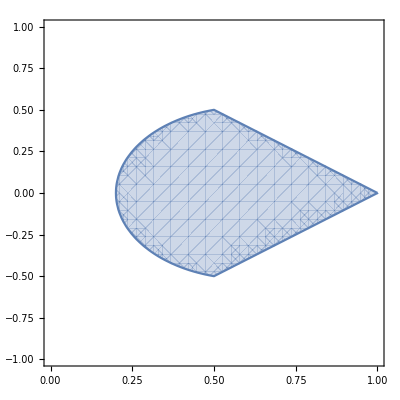

```mathematica
RegionPlot[1/5 ≤ x≤ 1&& y^2≤ (1-x)^2 && y^2≤ (1-x)(-1+5 x)/3,{x,0,1},{y,-1,1}]
```

```mathematica
N[1/√3]
```

0.57735

```mathematica
%/2
```

0.288675

```mathematica
(* EW biseparability conditions, applied on my coefficients: *)
```

```mathematica
fn[α_]:=3/4(1+5α)(1-3 α);
```

```mathematica
fn[-1/5]
```

0

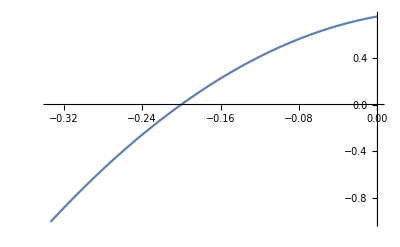

```mathematica
Plot[fn[x],{x,-1/3,0}]
```

```mathematica
fn[-1/6]
```

3/16